```mathematica
d1:=0.2;
d2:=0.07;
mu:=0.8;
cof:=0.001;
En[n_]:=√(cof*n+(d1+d2)^2);
2*Pi*d1*d2/cof;
En[700]
Mag[B_,T_]:=Cos[2*Pi*d1*d2/(cof*B)-Pi/4]*Sin[2*Pi*(mu^2-d1^2-d2^2)/(cof*B)]*(2*Pi^2*mu)/(cof*B)*T/Sinh[(2*Pi^2*mu*T)/(cof*B)];
Sig1[B_,T_]:=1 - 2/Pi*√((cof*B)/(d1*d2))*√(1 +((cof*B)/(Pi*d1*d2))^2)Cos[Pi*(mu^2-d1^2-d2^2)/(cof*B)]*Cos[2*Pi*(d1*d2)/(cof*B) + ArcTan[(cof*B)/(Pi*d1*d2)] - Pi/4]*(2*Pi^2*mu)/(cof*B)*T/Sinh[(2*Pi^2*mu*T)/(cof*B)];
Sig2[B_,T_]:= 1/Pi^2*(cof*B)/(d1*d2)*(1 + √(1 +((cof*B)/(Pi*d1*d2))^2)*Cos[4*Pi*(d1*d2)/(cof*B) + ArcTan[(cof*B)/(Pi*d1*d2)] - Pi/2]);
Plot[{Mag[B,10^-3], Sig1[B,10^-3] + Sig2[B,10^-3]}, {B,4,10}, PlotStyle->{Automatic, {Orange, Thick}}, Frame->True,PlotRange -> {-0.65, 1.85},FrameLabel->{Style["Magnetic field, T",10],Style["Rel.units",10]}, Epilog->{{Black,Text["Conductivity",{9.3,1.68},{-1,-1}]},
{Black,Text["Magnetization",{9.3,1.55},{-1,-1}]}, {Black,Text["Δ_S = 0.2 eV",{4.1,1.68},{-1,-1}]}, {Black,Text["Δ_D = 0.07 eV",{4.1,1.55},{-1,-1}]},
 {Black,Text["T = 11.6 K",{4.1,1.42},{-1,-1}]},
{Arrow[{{7.48, 0.35}, {7.48, 0.05}}]},
{Arrow[{{7.58,1.35}, {7.58,1.05}}]},
{Arrow[{{5.96,1.35}, {5.96,1.05}}]},
{Arrow[{{5.9,0.35}, {5.9,0.05}}]}}]
```

0.879147

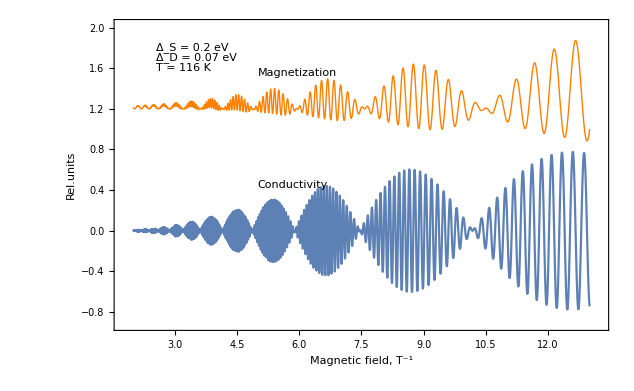

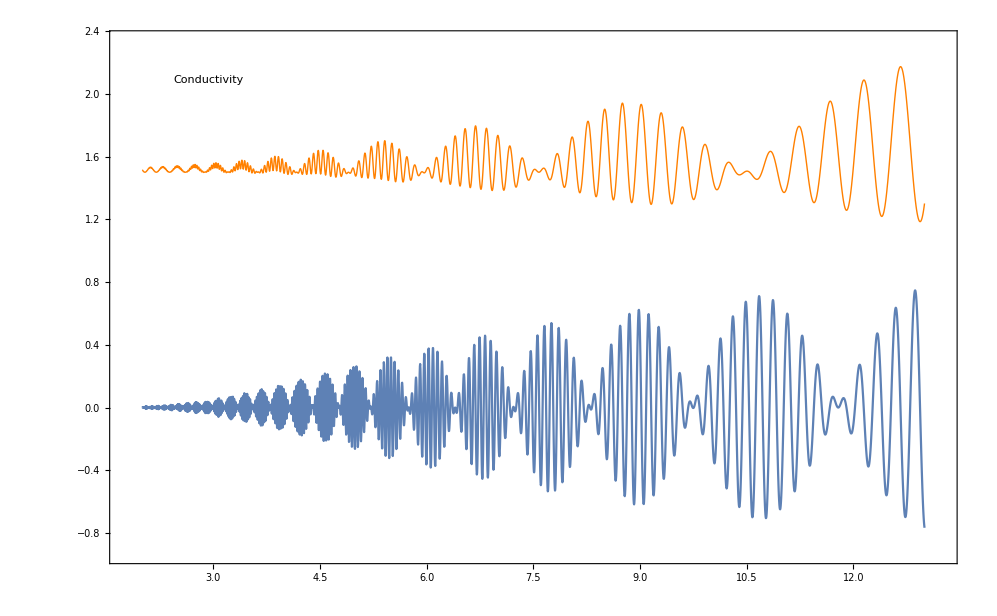

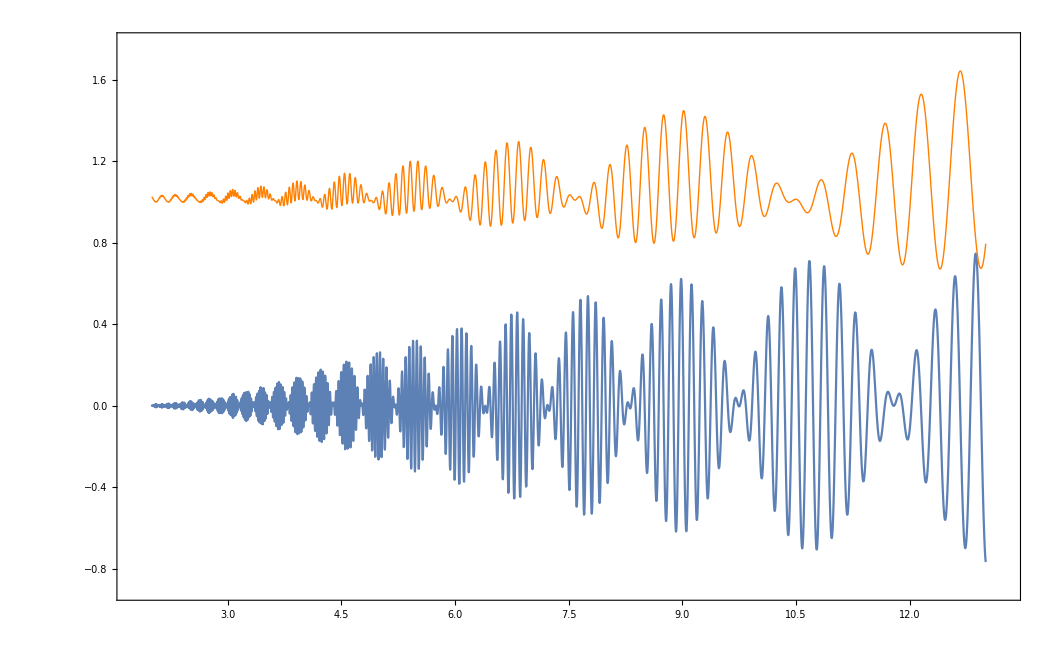

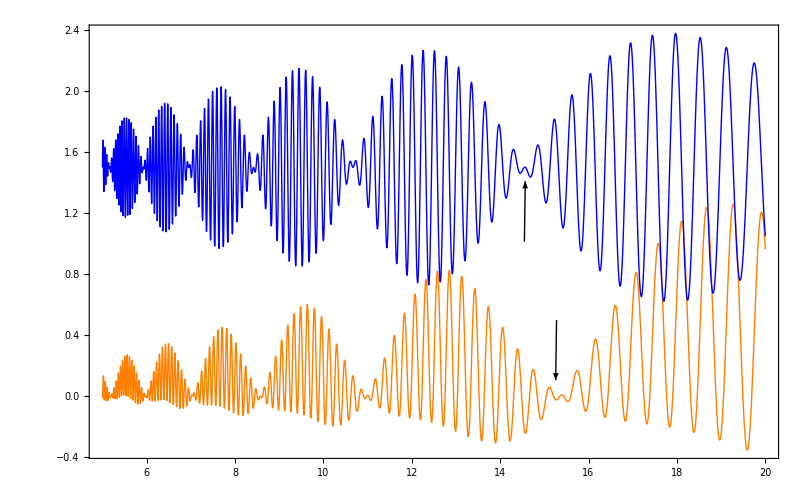

-Graphics-

```mathematica
16/0.138
```

115.942

```mathematica
Manipulate[Plot[{Sig[B,T], Mag[B,T]+2}, {B,5,20}, PlotStyle->{{Orange, Thick}, {Blue, Thick}}, Frame->True], {T,10^-4,10^-2}]
```